## Example 1

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
MatrixForm[P]
MatrixForm[A]
MatrixForm[B]
```

(1 | 1 | 1 | 1
1 | 1 | 1 | 0
1 | 1 | 0 | 1
0 | 1 | 1 | 0)

(39 | -27 | -9 | 5
9 | 3 | -9 | 5
22 | -27 | 8 | 5
9 | 0 | -9 | 8)

(8 | -2 | -4 | 5
4 | 2 | -4 | 5
-3 | -2 | 7 | 5
4 | 0 | -4 | 7)

Comprobación de que son simultáneamente diagonalizables A.B=B.A (Por la propia construcción de A y B sabemos que lo son)

```mathematica
MatrixForm[A.B]
MatrixForm[B.A]
```

(251 | -114 | -131 | 50
131 | 6 | -131 | 50
64 | -114 | 56 | 50
131 | 0 | -131 | 56)

(251 | -114 | -131 | 50
131 | 6 | -131 | 50
64 | -114 | 56 | 50
131 | 0 | -131 | 56)

Cálculo de f̃(t)

```mathematica
sol[t_]:={ⅇ^-t,Sin[t],2 t^2,1+t}
FullSimplify[D[sol[t],t]+A.sol[t]-B.sol[t-1]]
```

{ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))}

Cálculo de los valores y vectores propios de A

```mathematica
Eigenvectors[A]
```

{{1,0,1,0},{1,1,0,1},{1,1,1,1},{1,1,1,0}}

```mathematica
Eigenvalues[A]
```

{30,17,8,3}

Correspondencias:

```mathematica
Simplify[A.{1,0,1,0}]
```

{30,0,30,0}

```mathematica
Simplify[30*{1,0,1,0}]
```

{30,0,30,0}

```mathematica
Simplify[A.{1,1,0,1}]
```

{17,17,0,17}

```mathematica
Simplify[17*{1,1,0,1}]
```

{17,17,0,17}

```mathematica
Simplify[A.{1,1,1,1}]
```

{8,8,8,8}

```mathematica
Simplify[8*{1,1,1,1}]
```

{8,8,8,8}

```mathematica
Simplify[A.{1,1,1,0}]
```

{3,3,3,0}

```mathematica
Simplify[3*{1,1,1,0}]
```

{3,3,3,0}

Cálculo de los valores y vectores propios de B

```mathematica
Eigenvectors[B]
```

{{1,1,0,1},{1,1,1,1},{1,0,1,0},{1,1,1,0}}

```mathematica
Eigenvalues[B]
```

{11,7,4,2}

Correspondencias

```mathematica
Simplify[B.{1,0,1,0}]
```

{4,0,4,0}

```mathematica
Simplify[4*{1,0,1,0}]
```

{4,0,4,0}

```mathematica
Simplify[B.{1,1,0,1}]
```

{11,11,0,11}

```mathematica
Simplify[11*{1,1,0,1}]
```

{11,11,0,11}

```mathematica
Simplify[B.{1,1,1,1}]
```

{7,7,7,7}

```mathematica
Simplify[7*{1,1,1,1}]
```

{7,7,7,7}

```mathematica
Simplify[B.{1,1,1,0}]
```

{2,2,2,0}

```mathematica
Simplify[2*{1,1,1,0}]
```

{2,2,2,0}

Así tenemos que

```mathematica
λ1=3;(*valores propios A*)
λ2=8;
λ3=17;
λ4=30;
γ1=2;(*valores propios B*)
γ2=7;
γ3=11;
γ4=4;
v1={1,1,1,0};(*vectores propios comunes*)
v2={1,1,1,1};
v3={1,1,0,1};
v4={1,0,1,0};
μ1=γ1/λ1;
μ2=γ2/λ2;
μ3=γ3/λ3;
μ4=γ4/λ4;
```

```mathematica
N[μ1]
```

0.666667

```mathematica
N[μ2]
```

0.875

```mathematica
N[μ3]
```

0.647059

```mathematica
N[μ4](*Como este valor se encuentra en la región de estabilidad incondicional para ambos métodos podemos omitir sus cálculos*)
```

0.133333

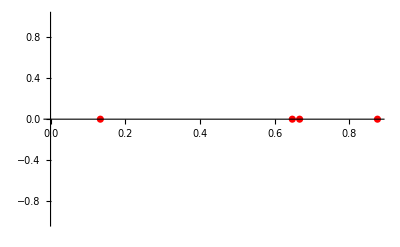

```mathematica
ListPlot[{{μ1,0},{μ2,0},{μ3,0},{μ4,0}}, PlotStyle->Red]
```

```mathematica
(*Para hallar la restricción del tamaño de paso para cada uno de los métodos es necesario calcular χ(Subscript[μ, i]) para el IMEX BDF2 y χ̃(Subscript[μ, i]) para el IMEX BDF3. Sabemos que para los valores de Subscript[μ, i] encontrados estas funciones definidas a trozos toman concretamente las funciones: *)
```

RESTRICCIÓN TAMAÑO DE PASO IMEX BDF2

```mathematica
χ2[r_]:=Solve[1+(-3-r^2) #1^2+(2-2 r^2) #1^3+4 r^4 #1^4==0,#1][[1]][[1]][[2]]
χ22[r_]:=4/(1-3r)
l2={Abs[N[χ2[μ1]]]/λ1,Abs[N[χ2[μ2]]]/λ2,Abs[N[χ2[μ3]]]/λ3,Abs[N[χ22[μ4]]]/λ4}
```

{0.957042,0.157609,0.185711,0.222222}

```mathematica
Min[l2](*Restricción del tamaño de paso para el IMEX BDF2*)
```

0.157609

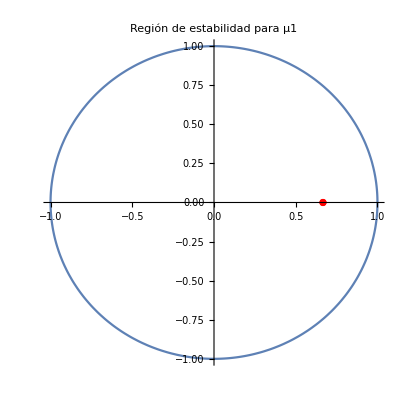

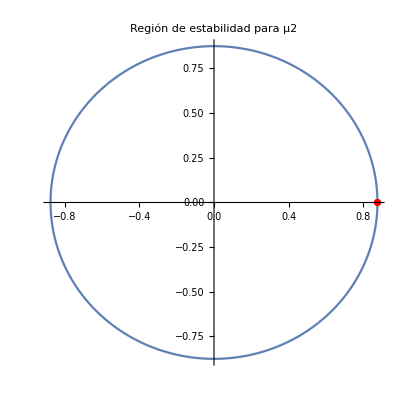

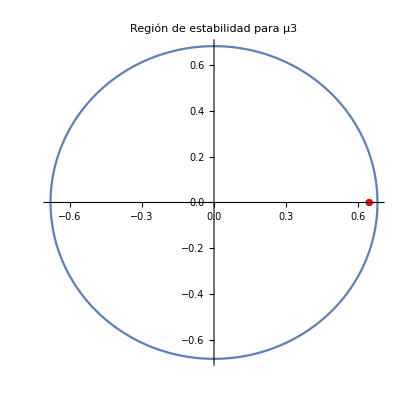

```mathematica
ψ2[z_]:=-(√(1+2z+√(-(-3+2z)(1+2z)(-5+8z))))/(2 √2 z)
regλ1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotLabel->"Región de estabilidad para μ1"];(*Como -λ1*Min[l2]=Subscript[z, 1] es menor que -1/(√2)se toma como función el 1 por la propia definicción de ψ(z)*)
regλ2=ParametricPlot[{ψ2[-λ2*Min[l2]]*Cos[t],ψ2[-λ2*Min[l2]]*Sin[t]},{t,0,2Pi},PlotLabel->"Región de estabilidad para μ2"];
regλ3=ParametricPlot[{ψ2[-λ3*Min[l2]]*Cos[t],ψ2[-λ3*Min[l2]]*Sin[t]},{t,0,2Pi},PlotLabel->"Región de estabilidad para μ3"];
mu1=ListPlot[{{μ1,0}},PlotStyle->Red];
mu2=ListPlot[{{μ2,0}},PlotStyle->Red];
mu3=ListPlot[{{μ3,0}},PlotStyle->Red];
Show[regλ1,mu1]
Show[regλ2,mu2]
Show[regλ3,mu3]
```

RESTRICCIÓN TAMAÑO DE PASO IMEX BDF3

```mathematica
FuncDistCuad[z_,θ_]:=(265-66 z+18 z^2+54 (-7+2 z) Cos[θ]-27 (-5+2 z) Cos[2 θ]-22 Cos[3 θ]+12 z Cos[3 θ])/(18 z^2 (19-24 Cos[θ]+6 Cos[2 θ]));
d[z_]:=Simplify[Solve[-3+(-14-12 z+72 z^2) #1+(32+12 z+216 z^2) #1^2+(94+60 z+216 z^2) #1^3+(-1357+804 z+72 z^2) #1^4==0,#1][[4]][[1]][[2]]];

Funθ4[z_]:=Sqrt[FuncDistCuad[z,θ]/.{θ->Simplify[2*ArcTan[Sqrt[d[z]]]]}];
χ32[r_]:=-20/(3(7r-1))
```

```mathematica
l3={Abs[Re[FindRoot[Funθ4[z]==μ1,{z,-1}][[1,2]]]]/λ1,Abs[Re[FindRoot[Funθ4[z]==μ2,{z,-1}][[1,2]]]]/λ2,Abs[Re[FindRoot[Funθ4[z]==μ3,{z,-1}][[1,2]]]]/λ3,Abs[N[χ32[μ4]]]/λ4}
```

{0.412653,0.107022,0.0760254,3.33333}

```mathematica
Min[l3](*Restricción del tamaño de paso para el IMEX BDF3*)
```

0.0760254

-Graphics-

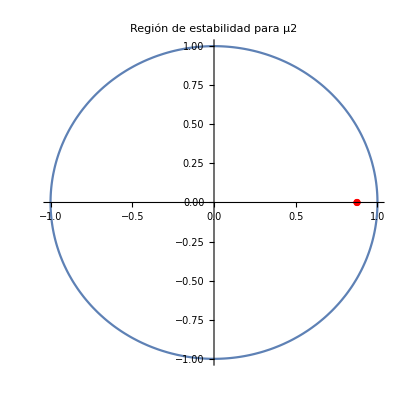

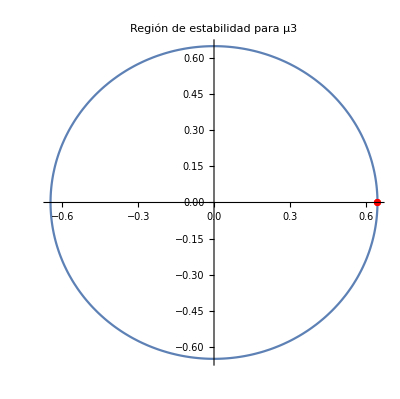

```mathematica
regλ1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotLabel->"Región de estabilidad para μ1"];(*Como -λ1*Min[l3]=Subscript[z, 1] es menor que -0.723se toma como función el 1 por la propia definicción de ψ̃(z)*)
regλ2=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotLabel->"Región de estabilidad para μ2"];
regλ3=ParametricPlot[{Funθ4[-λ3*Min[l3]]*Cos[t],Funθ4[-λ3*Min[l3]]*Sin[t]},{t,0,2Pi},PlotLabel->"Región de estabilidad para μ3"];
mu1=ListPlot[{{μ1,0}},PlotStyle->Red];
mu2=ListPlot[{{μ2,0}},PlotStyle->Red];
mu3=ListPlot[{{μ3,0}},PlotStyle->Red];
Show[regλ1,mu1]
Show[regλ2,mu2]
Show[regλ3,mu3]
```

Resolución mediante el método IMEX BDF2

```mathematica
(*h=0.5*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/2;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[Length[A]]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{4.87929×10^44,4.87929×10^44,4.87929×10^44,4.87929×10^44}

```mathematica
(*h=0.25*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/4;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[Length[A]]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{1.34834×10^21,1.34834×10^21,1.34834×10^21,1.34834×10^21}

```mathematica
(*h=0.1*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/10;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[Length[A]]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.200873,0.19977,0.274206,0.206667}

```mathematica
(*h=0.05*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/20;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[Length[A]]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.0501958,0.0499337,0.0685291,0.0516667}

```mathematica
(*h=0.025*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/40;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[Length[A]]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.012547,0.0124832,0.0171303,0.0129167}

```mathematica
(*h=0.01*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/100;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[Length[A]]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.00200735,0.00199732,0.00274069,0.00206666}

```mathematica
(*h=0.005*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/200;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[Length[A]]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.000501829,0.000499335,0.000685163,0.000516668}

Ratios de convergencia

```mathematica
Norm[{0.05019580467342166,0.049933745102103855,0.06852913822513074,0.0516666673211148}]
```

0.11126

```mathematica
Norm[{0.0005018294387753031,0.0004993351769915777,0.000685162958689034,0.0005166678129171487}]
```

0.00111246

```mathematica
Log[0.05/0.005,0.11125953893794459/0.001112457780532298](*Ratio de convergencia con IMEX BDF2*)
```

2.00005

Cálculo mediante el Teorema 19 (restricción de tamaño de paso)

```mathematica
χ2[r_]:=Solve[1+(-3-r^2) #1^2+(2-2 r^2) #1^3+4 r^4 #1^4==0,#1][[1]][[1]][[2]]
χ22[r_]:=4/(1-3r)
l2={Abs[N[χ2[μ1]]]/λ4,Abs[N[χ2[μ2]]]/λ4,Abs[N[χ2[μ3]]]/λ4,Abs[N[χ22[μ4]]]/λ4}
```

{0.0957042,0.0420291,0.105236,0.222222}

```mathematica
Min[l2]
```

0.0420291

```mathematica
(*La restricción ahora es 0.0420291 cuando por la Proposición 17 era 0.157609*)
```

Resolución mediante el método IMEX BDF3

```mathematica
(*h=0.5*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/2;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[Length[A]]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{4.55527×10^119,4.55527×10^119,4.57185×10^119,4.55527×10^119}

```mathematica
(*h=0.25*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/4;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[Length[A]]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{2.03284×10^98,2.03284×10^98,8.49918×10^83,2.03284×10^98}

```mathematica
(*h=0.1*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/10;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[Length[A]]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{5.00252×10^22,5.00252×10^22,4.45402×10^7,5.00252×10^22}

```mathematica
(*h=0.05*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/20;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[Length[A]]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{0.0000156043,2.25345×10^-6,0.0000156046,4.51109×10^-10}

```mathematica
(*h=0.025*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/40;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[Length[A]]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{1.62323×10^-6,1.05145×10^-7,1.6233×10^-6,5.02041×10^-10}

```mathematica
(*h=0.01*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/100;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[Length[A]]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{9.61735×10^-8,1.66313×10^-8,9.7265×10^-8,4.311×10^-9}

```mathematica
(*h=0.005*)
```

```mathematica
P={{1,1,1,1},{1,1,1,0},{1,1,0,1},{0,1,1,0}};
A=P.{{3,0,0,0},{0,8,0,0},{0,0,17,0},{0,0,0,30}}.Inverse[P];
B=P.{{2,0,0,0},{0,7,0,0},{0,0,11,0},{0,0,0,4}}.Inverse[P];
τ=1;
h=1/200;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={E^-t,Sin[t],2 t^2,1+t};
y0=sol[t0];
fTilde[t_]:={ⅇ^-t (38-8 ⅇ-ⅇ^t (-13+2 t (8+5 t)+2 Sin[1-t]+27 Sin[t])),ⅇ^-t (9-4 ⅇ+ⅇ^t (13-2 t (8+5 t)+Cos[t]+2 Sin[1-t]+3 Sin[t])),-9+ⅇ^-t (22+3 ⅇ)+2 t (16+t)-2 Sin[1-t]-27 Sin[t],ⅇ^-t (9-4 ⅇ+ⅇ^t (17-5 t (3+2 t)))};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[Length[A]]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{5.36107×10^-9,1.95439×10^-8,8.61473×10^-9,1.62545×10^-8}

Ratio de convergencia

```mathematica
Norm[{0.0000156043388415128,2.253445776589924*^-6,0.00001560460077598691,4.511093720793724*^-10}]
```

0.0000221828

```mathematica
Norm[{5.361073363019386*^-9,1.954388478830893*^-8,8.614733815193176*^-9,1.6254489310085773*^-8}]
```

2.73702×10^-8

```mathematica
Log[0.05/0.005,0.000022182808075854757/2.7370177231079353*^-8](*Ratio de convergencia con IMEX BDF3*)
```

2.90874

Cálculo mediante el Teorema 19 (restricción de tamaño de paso)

```mathematica
FuncDistCuad[z_,θ_]:=(265-66 z+18 z^2+54 (-7+2 z) Cos[θ]-27 (-5+2 z) Cos[2 θ]-22 Cos[3 θ]+12 z Cos[3 θ])/(18 z^2 (19-24 Cos[θ]+6 Cos[2 θ]));
d[z_]:=Simplify[Solve[-3+(-14-12 z+72 z^2) #1+(32+12 z+216 z^2) #1^2+(94+60 z+216 z^2) #1^3+(-1357+804 z+72 z^2) #1^4==0,#1][[4]][[1]][[2]]];

Funθ4[z_]:=Sqrt[FuncDistCuad[z,θ]/.{θ->Simplify[2*ArcTan[Sqrt[d[z]]]]}];
χ32[r_]:=-20/(3(7r-1))
```

```mathematica
l3={Abs[Re[FindRoot[Funθ4[z]==μ1,{z,-1}][[1,2]]]]/λ4,Abs[Re[FindRoot[Funθ4[z]==μ2,{z,-1}][[1,2]]]]/λ4,Abs[Re[FindRoot[Funθ4[z]==μ3,{z,-1}][[1,2]]]]/λ4,Abs[N[χ32[μ4]]]/λ4}
```

{0.0412653,0.0285391,0.0430811,3.33333}

```mathematica
Min[l3]
```

0.0285391

```mathematica
(*La restricción ahora es 0.0285391 cuando por la Proposición 17 era 0.0760254*)
```